Autor: Radosław Terelak

# Metody numeryczne

## (kierunek Informatyka)

## Projekt 8

Metoda Eulera

Napisać procedurę realizującą algorytm metody Eulera (argumenty:  f, x_0, y_0, b, n).

a) Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=(y(x))/x^2      dla x∈[1,10],
y(1)=2.

Obliczenia wykonać dla 40 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązanie przybliżone.
Wykreślić także błędy uzyskanego rozwiązania przybliżonego.

## Rozwiązanie

### Program

```mathematica
ClearAll["Global`*"];
euler[f_,x0_,y0_,b_,l_] := Module[{i=1,h,yo= {y0},xo = {x0},dok,err={},n=l-1},
h = (b-x0)/n;
While[i<=n,
AppendTo[yo,N[yo[[i]]+(h*f[xo[[i]],yo[[i]]])]];
AppendTo[xo,N[xo[[i]]+h]];
i++;
];
dok=DSolve[{u'[x]==f[x,u[x]],u[x0]==y0},u[x],x][[1,1,2]];
Print[Show[Plot[dok,{x,x0,b}],ListPlot[Transpose[{xo,yo}],PlotStyle->Red, PlotMarkers->{Automatic,3}]]];

i =1;
While[i <= n,
AppendTo[err,{xo[[i]],N[Abs[N[dok/.x->xo[[i]]]-yo[[i]]]]}];
i++;
];
Print[Show[ListPlot[err],PlotMarkers->{Automatic,3}]];
];
```

### Zadanie a)

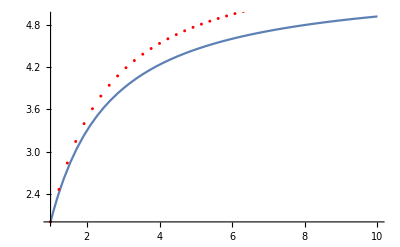

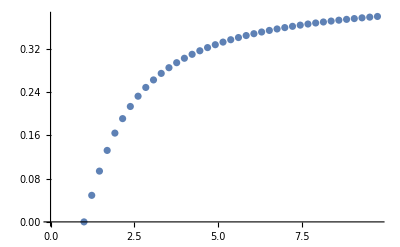

```mathematica
f[x_,y_]:=y/x^2;
euler[f,1,2,10,40]
```